## Project 2: Rigid-body dynamics

### Task 1

```mathematica
ClearAll["Global`*"];
```

```mathematica
tau[t_,Eps_,M_]:=t*Sqrt[(I3-I2)*(M^2-2*Eps*I1)/(I1*I2*I3)]
k2[Eps_,M_]:=(I2-I1)*(2*Eps*I3-M^2)/((I3-I2)(M^2-2*Eps*I1))
```

```mathematica
J1[tau_,k2_]:=JacobiCN[tau,k2]
J2[tau_,k2_]:=JacobiSN[tau,k2]
J3[tau_,k2_]:=JacobiDN[tau,k2]
```

```mathematica
wmega1[tau_,k2_,M_,Eps_]:=Sqrt[(2*Eps*I3-M^2)/(I1*(I3-I1))]*J1[tau,k2]
wmega2[tau_,k2_,M_,Eps_]:=Sqrt[(2*Eps*I3-M^2)/(I2*(I3-I2))]*J2[tau,k2]
wmega3[tau_,k2_,M_,Eps_]:=Sqrt[(M^2-2*Eps*I1)/(I3*(I3-I1))]*J3[tau,k2]
```

```mathematica
I1=0.8;
I2=0.9;
I3=1;
w1o=1;
w2o=0;
w3o=2;
tmax=100;
```

```mathematica
Eps0=(I1*w1o^2+I2*w2o^2+I3*w3o^2)/2;
M0=Sqrt[I1^2*w1o^2+I2^2*w2o^2+I3^2*w3o^2];
```

1. JacobiCN[0.333333 t,0.2]

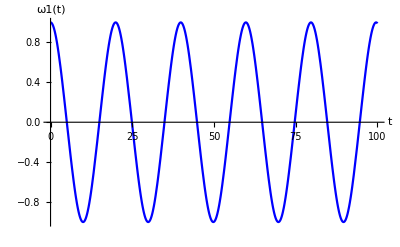

```mathematica
wmega1[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0]
Plot[wmega1[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0],{t,0,tmax},PlotStyle->Blue,AxesLabel->{t,ω1[t]}]
```

1.33333 JacobiSN[0.333333 t,0.2]

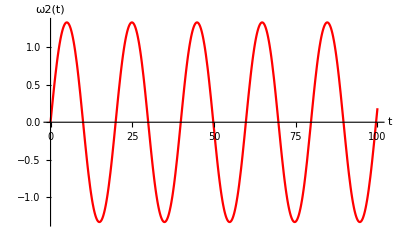

```mathematica
wmega2[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0]
Plot[wmega2[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0],{t,0,tmax},PlotStyle->Red,AxesLabel->{t,ω2[t]}]
```

2. JacobiDN[0.333333 t,0.2]

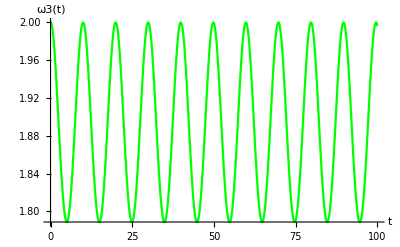

```mathematica
wmega3[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0]
Plot[wmega3[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0],{t,0,tmax},PlotStyle->Green,AxesLabel->{t,ω3[t]}]
```

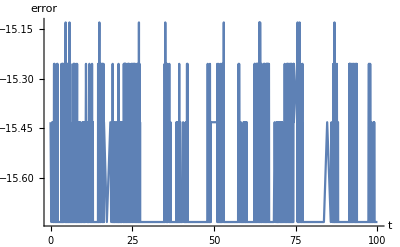

```mathematica
Epsilon[t_]:=(I1*wmega1[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0]^2+I2*wmega2[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0]^2+I3*wmega3[tau[t,Eps0,M0],k2[Eps0,M0],M0,Eps0]^2)/2;
errorE[t_]:=Log[10,Abs[(Epsilon[t]-Eps0)/Eps0]]
plot1=Plot[errorE[t],{t,0,tmax},AxesLabel->{t,error}]
```

### Task 2

```mathematica
Clear[t]
```

```mathematica
h=0.1;
n=IntegerPart[100/h];
```

```mathematica
t=ConstantArray[0,n];
w1=Array[0,n];
w2=Array[0,n];
w3=Array[0,n];
```

```mathematica
w1[[1]]=w1o;
w2[[1]]=w2o;
w3[[1]]=w3o;
```

```mathematica
w1t[t_,w2_,w3_]:=(I2-I3)*w2*w3/I1
w2t[t_,w1_,w3_]:=(I3-I1)*w3*w1/I2
w3t[t_,w1_,w2_]:=(I1-I2)*w1*w2/I3
```

```mathematica
For[i=1, i<n,i++,
{ rk0=h*w1t[t[[i]],w2[[i]],w3[[i]]];
rl0=h*w2t[t[[i]],w1[[i]],w3[[i]]];
rf0=h*w3t[t[[i]],w1[[i]],w2[[i]]];

rk1=h*w1t[t[[i]]+h/2,w2[[i]]+rl0/2,w3[[i]]+rf0/2];
rl1=h*w2t[t[[i]]+h/2,w1[[i]]+rk0/2,w3[[i]]+rf0/2];
rf1=h*w3t[t[[i]]+h/2,w1[[i]]+rk0/2,w2[[i]]+rl0/2];

rk2=h*w1t[t[[i]]+h/2,w2[[i]]+rl1/2,w3[[i]]+rf1/2];
rl2=h*w2t[t[[i]]+h/2,w1[[i]]+rk1/2,w3[[i]]+rf1/2];
rf2=h*w3t[t[[i]]+h/2,w1[[i]]+rk1/2,w2[[i]]+rl1/2];

rk3=h*w1t[t[[i]]+h,w2[[i]]+rl2,w3[[i]]+rf2];
rl3=h*w2t[t[[i]]+h,w1[[i]]+rk2,w3[[i]]+rf2];
rf3=h*w3t[t[[i]]+h,w1[[i]]+rk2,w2[[i]]+rl2];

w1[[i+1]]=w1[[i]]+(1/6)*(rk0+2*rk1+2*rk2+rk3);
w2[[i+1]]=w2[[i]]+(1/6)*(rl0+2*rl1+2*rl2+rl3);
w3[[i+1]]=w3[[i]]+(1/6)*(rf0+2*rf1+2*rf2+rf3);
t[[i+1]]=t[[i]]+h;
}
]
```

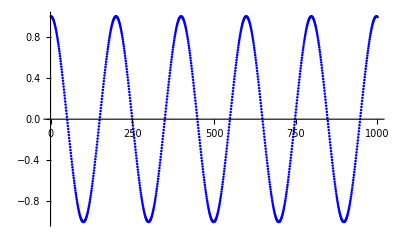

```mathematica
ListPlot[w1,PlotStyle->Blue]
```

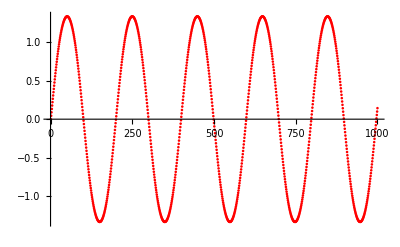

```mathematica
ListPlot[w2,PlotStyle->Red]
```

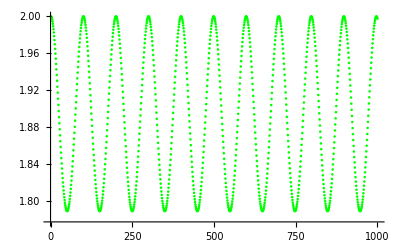

```mathematica
ListPlot[w3,PlotStyle->Green]
```

```mathematica
EpsRung=ConstantArray[0,n];
errorERung=ConstantArray[0,n];
EpsRung[[1]]=Eps0;
For[j=1,j< n,j++
{
EpsRung[[j]]=(I1*w1[[j]]^2+I2*w2[[j]]^2+I3*w3[[j]]^2)/2;
errorERung[[j]]=Log[10,Abs[(EpsRung[[j]]-Eps0)/Eps0]]
}]
```

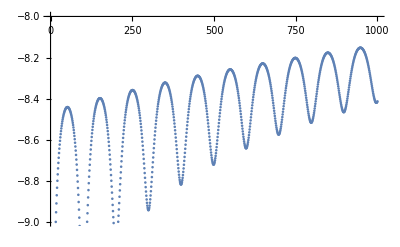

```mathematica
plot2=ListPlot[errorERung,PlotRange->{{0,1000},{-9,-8}}]
```

We observe that in the Runge-Kutta method the error in the energy increases as the iterations  are increasing (and oscillating) and of course comparing to the analytical solution that the errors come only from the errors of the computer, are much higher.

### Task 3

```mathematica
ClearAll["Global`*"];
```

```mathematica
dt=0.02;
n=5000;
```

```mathematica
Rx[theta_]:={{1,0,0},{0,Cos[theta],Sin[theta]},{0,-Sin[theta],Cos[theta]}};
Ry[theta_]:={{Cos[theta],0,-Sin[theta]},{0,1,0},{Sin[theta],0,Cos[theta]}};
Rz[theta_]:={{Cos[theta],Sin[theta],0},{-Sin[theta],Cos[theta],0},{0,0,1}};
```

```mathematica
M1o=0.8;
M2o=0;
M3o=2;
I1=0.8;
I2=0.9;
I3=1;
w1o=1;
w2o=0;
w3o=2;
```

```mathematica
M1=Array[0,n];
M2=Array[0,n];
M3=Array[0,n];
M1[[1]]=M1o;
M2[[1]]=M2o;
M3[[1]]=M3o;
```

```mathematica
Mx[t_,M1_,M2_,M3_]:=Rx[(M1/I1)*t].{M1,M2,M3}
My[t_,M1_,M2_,M3_]:=Ry[(M2/I2)*t].{M1,M2,M3}
Mz[t_,M1_,M2_,M3_]:=Rz[(M3/I3)*t].{M1,M2,M3}
```

```mathematica
For[f=1,f<n,f++,
{
a=Mx[dt/2,M1[[f]],M2[[f]],M3[[f]]];
b=My[dt/2,a[[1]],a[[2]],a[[3]]];
c=Mz[dt,b[[1]],b[[2]],b[[3]]];
d=My[dt/2,c[[1]],c[[2]],c[[3]]];
e=Mx[dt/2,d[[1]],d[[2]],d[[3]]];
M1[[f+1]]=e[[1]];
M2[[f+1]]=e[[2]];
M3[[f+1]]=e[[3]];
}
]
```

```mathematica
w1=M1/I1;
w2=M2/I2;
w3=M3/I3;
```

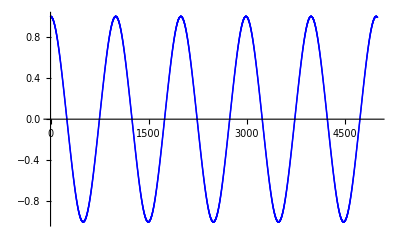

```mathematica
ListPlot[w1,PlotStyle->Blue]
```

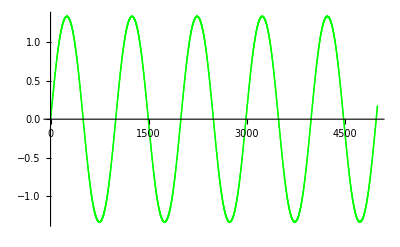

```mathematica
ListPlot[w2,PlotStyle->Green]
```

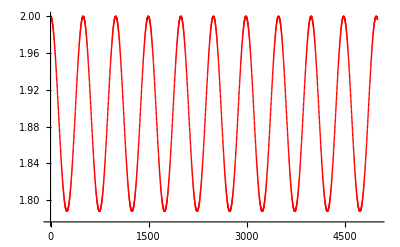

```mathematica
ListPlot[w3,PlotStyle->Red]
```

```mathematica
Epssplit=ConstantArray[0,n];
errorsplit=ConstantArray[0,n];
Eps0=(I1*w1o^2+I2*w2o^2+I3*w3o^2)/2;
Epssplit[[1]]=Eps0;

For[j=2,j<n,j++
{
Epssplit[[j]]=(I1*w1[[j]]^2+I2*w2[[j]]^2+I3*w3[[j]]^2)/2;
errorsplit[[j]]=Log[10,Abs[(Epssplit[[j]]-Eps0)/Eps0]]
}]
```

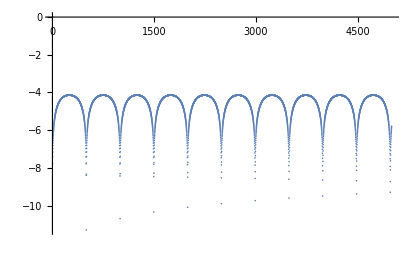

```mathematica
ListPlot[errorsplit,PlotRange->All]
```

We observe that at some points the error in the energy almost goes to zero (in the log diagram goes to infinity) and it is oscilating but not increasing through the time as the error in the Runge-Kutta does.